# Tension between SN and BAO datasets

## Created by C. Escamilla-Rivera. March 2017

You are free to use, distribute, and modify this code, as long as you cite the respective papers/references:
(I) Tension between SN and BAO: current status and future forecasts. JCAP 1109 (2011) 003

Can I modify the code? 
Yes, you can. In fact, I actively encourage it! It would be great if you could release any modifications that you make to the code, so that they can be shared by everyone. I’m not a stickler about it, though, as long as: (a) you’re nice about it, (b) make good faith attempts to describe and/or share your modifications if asked, and (c) you give proper credit.

But please do email me if you get stuck: cescamilla@mctp.mx

```mathematica
SetDirectory["/Users/celiaescamilla/Desktop"];
```

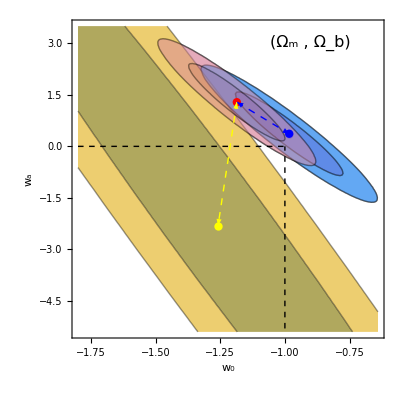

```mathematica
omi=0.237;
obi=0.0405;
ome=0.023;
obe=0.0039;

(*p:priors*)

omp:=omi;
obp:=obi;

(*omp:=omi+ome;*)
(*obp:=obi+obe;*)

(*omp:=omi-ome;*)
(*obp:=obi-obe;*)

(*SN data results*)
(*Add the respective files with the results of the best fits and the covariance matrix by columns*)

CovSN=Get["covsn.txt"];
meSN=Get["bestfitsn.txt"][[2]];
FisSN=Inverse[CovSN];
v[x_,y_]={x,y};
me[i_,j_]:={meSN[[i]],meSN[[j]]};
f[x_,y_,i_,j_]:=(v[x,y]-me[i,j]).FisSN.(v[x,y]-me[i,j]);
SN=FixPolygons[ContourPlot[f[x,y,1,2],{x,-1.8,-0.64},{y,-5.4,3.5},Contours->{2.30,6.17},ContourShading->{{ColorData["DeepSeaColors"][0.6],Opacity[0.6]},{ColorData["DeepSeaColors"][0.7],Opacity[0.6]},Opacity[0.]},FrameLabel->{Subscript[w,0],Subscript[w, a]}]];
bestSN={{meSN[[1]],meSN[[2]]}};
pbestSN=ListPlot[bestSN,PlotStyle->{Blue,PointSize[0.015]}];
Show[SN,pbestSN];

(*BAO data results*)

CovBAO=Get["covbao.txt"];
meBAO=Get["bestfitbao.txt"][[2]];
FisBAO=Inverse[CovBAO];
v[x_,y_]={x,y};
me[i_,j_]:={meBAO[[i]],meBAO[[j]]};
f[x_,y_,i_,j_]:=(v[x,y]-me[i,j]).FisBAO.(v[x,y]-me[i,j]);
BAO=FixPolygons[ContourPlot[f[x,y,1,2],{x,-1.8,-0.64},{y,-5.4,3.5},Contours->{2.30,6.17},ContourShading->{{ColorData["SandyTerrain"][0.8],Opacity[0.8]},{ColorData["SandyTerrain"][0.6],Opacity[0.8]},Opacity[0.]},FrameLabel->{Subscript[w,0],Subscript[w, a]}]];
bestBAO={{meBAO[[1]],meBAO[[2]]}};
pbestBAO=ListPlot[bestBAO,PlotStyle->{Yellow,PointSize[0.015]}];
Show[BAO,pbestBAO];

(*SN+BAO data results*)
CovTOT=Get["covtotal.txt"];
meTOT=Get["bestfittotal.txt"][[2]];
FisTOT=Inverse[CovTOT];
v[x_,y_]={x,y};
me[i_,j_]:={meTOT[[i]],meTOT[[j]]};
f[x_,y_,i_,j_]:=(v[x,y]-me[i,j]).FisTOT.(v[x,y]-me[i,j]);
TOT=FixPolygons[ContourPlot[f[x,y,1,2],{x,-1.8,-0.64},{y,-5.4,3.5},Contours->{2.30,6.17},ContourShading->{{ColorData["ValentineTones"][0.6],Opacity[0.5]},{ColorData["ValentineTones"][0.7],Opacity[0.5]},Opacity[0.]},FrameLabel->{"\!\(\*SubsuperscriptBox[\"w\", \"0\", \"\"]\)",Rotate["\!\(\*SubsuperscriptBox[\"w\", \"a\", \"\"]\)",-90Degree]},LabelStyle->Directive[FontFamily-> "Helvetica",Italic,FontSize->12]]];
bestTOT={{meTOT[[1]],meTOT[[2]]}};
pbestTOT=ListPlot[bestTOT,PlotStyle->{Red,PointSize[0.015]}];

(*Comparison with LCDM model*)
lcdm=Graphics[{Dashing[{0.01,0.01}],Line[{{-1.0,-5.3},{-1.0,0}}],Line[{{-1.8,0},{-1.0,0}}]}];

frS = Graphics[{Arrowheads[{-.03, .03}],Dashed, Blue,Arrow[{{meTOT[[1]],meTOT[[2]]}, {meSN[[1]],meSN[[2]]}}]}];
frB = Graphics[{Arrowheads[{-.03, .03}], Dashed,Yellow,Arrow[{{meTOT[[1]],meTOT[[2]]}, {meBAO[[1]],meBAO[[2]]}}]}];
frL = Graphics[{Arrowheads[{-.03, .03}], Arrow[{{meTOT[[1]],meTOT[[2]]}, {-1,0}}]}];
pfrS=Graphics[Text[Style["(\!\(\*SubsuperscriptBox[\"Ω\", \"m\", \"\"]\) , \!\(\*SubsuperscriptBox[\"Ω\", \"b\", \"\"]\))",FontFamily-> "Helvetica",Italic,FontSize->16],{-0.9,3.0}]];

total=Show[TOT,SN,pbestSN,BAO,SN,TOT,pbestBAO,pbestSN,pbestTOT,lcdm,frS,frB,pfrS]
```